# qLanth : M1 Transitions

```mathematica
Exit[]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["qlanth.m"];
Get["misc.m"];
Get["qonstants.m"];
```

## The Magnetic Dipole Operator

### gs = 1 simply gives an operator proportional to J

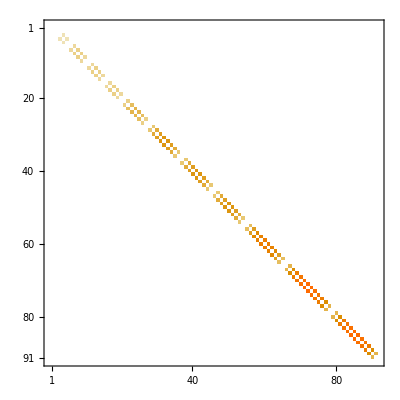

-Graphics-

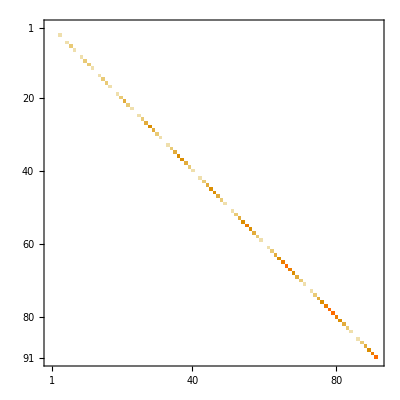

```mathematica
numE=2;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->1}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
Jx=-2*magx;
Jy=-2*magy;
Jz=-2*magz;
Jop={Jx,Jy,Jz};
MatrixPlot[Abs[Jx]]
MatrixPlot[Abs[Jy]]
MatrixPlot[Abs[Jz]]
```

We can check to see if the commutator relationships check out.

```mathematica
Commutator[op1_,op2_]:=op1.op2-op2.op1;
permutations=Permutations[{1,2,3}];
Table[
(
{idx1,idx2,idx3}=permutation;
sign=Signature[permutation];
Max@Flatten[Abs[Commutator[Jop[[idx1]],Jop[[idx2]]]-I  sign*Jop[[idx3]]]]
)
,{permutation,permutations}]
```

{0,0,0,0,0,0}

Manual check on numE=2

```mathematica
TFun=Transpose;
idx=3;
prettybasis[[idx]]
{a,b}={1,1};
Print["jx : ",Simplify[a(prettybasis).TFun[Jx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[Jy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[Jz][[idx]]]]
idx=idx+1;
prettybasis[[idx]]
Print["jx : ",Simplify[a(prettybasis).TFun[Jx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[Jy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[Jz][[idx]]]]
idx=idx+1;
prettybasis[[idx]]
Print["jx : ",Simplify[a(prettybasis).TFun[Jx][[idx]]]]
Print["jy : ",Simplify[b(prettybasis).TFun[Jy][[idx]]]]
Print["jz : ",Simplify[(prettybasis).TFun[Jz][[idx]]]]
```

3P{1,-1}

jx : (3P{1,0})/(√2)

jy : -(ⅈ 3P{1,0})/(√2)

jz : -3P{1,-1}

3P{1,0}

jx : (3P{1,-1}+3P{1,1})/(√2)

jy : (ⅈ (3P{1,-1}-3P{1,1}))/(√2)

jz : 0

3P{1,1}

jx : (3P{1,0})/(√2)

jy : (ⅈ 3P{1,0})/(√2)

jz : 3P{1,1}

The spectrum of the resultant matrices should match the spectrum for Jx, Jy, Jz, and J^2.

```mathematica
Off[Eigenvalues::arh];
numE=2;
eigenTruth={"J^2s",N[(#*(#+1))]&/@AllowedJ[numE]}
{"MJs",N[Sort[DeleteDuplicates[Flatten[AllowedMforJ/@AllowedJ[numE]]]]]}
magOp=ReplaceInSparseArray[#,{gs->1}]&/@MagDipoleMatrixAssembly[numE];
{Jx,Jy,Jz}=-2*magOp;
Jsquared=Simplify[ Jx.Jx+ Jy.Jy+Jz.Jz];
{"J^2s*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jsquared]]//Chop,0.001]]}
{"MJxs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jx]]//Chop,0.001]]}
{"MJys*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jy]]//Chop,0.001]]}
{"MJzs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Jz]]//Chop,0.001]]}
```

{J^2s,{0.,2.,6.,12.,20.,30.,42.}}

{MJs,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{J^2s*,{0.,2.,6.,12.,20.,30.,42.}}

{MJxs*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{MJys*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{MJzs*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

### gs = 0 simply gives an operator proportional to L

Putting gs=0 should lead to matrix spectrum of L.

```mathematica
Off[Eigenvalues::arh];
numE=2;
allowedL=DeleteDuplicates[Sort[Last/@FindSL/@First/@AllowedNKSLJTerms[numE]]];
eigenTruth={"L^2s",N[(#*(#+1))]&/@allowedL}
{"MLs",N[DeleteDuplicates[Sort[Flatten[Range[-#,#]&/@allowedL]]]]}
magOp=ReplaceInSparseArray[#,{gs->0}]&/@MagDipoleMatrixAssembly[numE];
{Lx,Ly,Lz}=-2*magOp;
Lsquared=Simplify[ Lx.Lx+ Ly.Ly+Lz.Lz];
{"L^2s*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lsquared]]//Chop,0.001]]}
{"MLxs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lx]]//Chop,0.001]]}
{"MLys*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Ly]]//Chop,0.001]]}
{"MLzs*",Sort@DeleteDuplicates[Round[Eigenvalues[N[Lz]]//Chop,0.001]]}
```

{L^2s,{0.,2.,6.,12.,20.,30.,42.}}

{MLs,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{L^2s*,{0.,2.,6.,12.,20.,30.,42.}}

{MLxs*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{MLys*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

{MLzs*,{-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.}}

### gs = very large simply gives an operator proportional to S

Putting gs = very-large should converge to the spectrum of the total spin S.

```mathematica
Off[Eigenvalues::arh];
numE=2;
η=10^10;
allowedS=DeleteDuplicates[Sort[First/@FindSL/@First/@AllowedNKSLJTerms[numE]]];
eigenTruth={"S^2s",N[(#*(#+1))]&/@allowedS}
{"MSs",N[DeleteDuplicates[Sort[Flatten[Range[-#,#]&/@allowedS]]]]}
magOp=ReplaceInSparseArray[#,{gs->η}]&/@MagDipoleMatrixAssembly[numE];
{Sx,Sy,Sz}=-2*magOp;
Ssquared=Simplify[ Sx.Sx+ Sy.Sy+Sz.Sz];
{"S^2s*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Ssquared]]//Chop,0.001]]}
{"MSxs*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sx]]//Chop,0.001]]}
{"MSys*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sy]]//Chop,0.001]]}
{"MSzs*",1/η Sort@DeleteDuplicates[Round[Eigenvalues[N[Sz]]//Chop,0.001]]}
```

{S^2s,{0.,2.}}

{MSs,{-1.,0.,1.}}

{S^2s*,{0.,6.×10^-10,2.×10^-9,4.2×10^-9,2.×10^10,2.×10^10,2.×10^10,2.×10^10,2.×10^10,2.×10^10,2.×10^10}}

{MSxs*,{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-6.×10^-10,-5.×10^-10,-4.×10^-10,-3.×10^-10,-2.×10^-10,-1.×10^-10,0.,1.×10^-10,2.×10^-10,3.×10^-10,4.×10^-10,5.×10^-10,6.×10^-10,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

{MSys*,{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-6.×10^-10,-5.×10^-10,-4.×10^-10,-3.×10^-10,-2.×10^-10,-1.×10^-10,0.,1.×10^-10,2.×10^-10,3.×10^-10,4.×10^-10,5.×10^-10,6.×10^-10,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

{MSzs*,{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-6.×10^-10,-5.×10^-10,-4.×10^-10,-3.×10^-10,-2.×10^-10,-1.×10^-10,0.,1.×10^-10,2.×10^-10,3.×10^-10,4.×10^-10,5.×10^-10,6.×10^-10,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

## Pr in LaF3

Using this we can compute the magnetic dipole (M1) transition rates and oscillator strengths.
Here we show an example using the case of Pr^(3+) in LaF3.

```mathematica
numE=2;
{rmsDifference,carnallEnergies,eigenEnergies,ln,
carnallAssignments,simplerStateLabels,eigensys,basis,truncatedStates}=Import["./calcs/Pr in LaF3 - example.m"];
eigenEnergies=eigenEnergies-eigenEnergies[[1]];
```

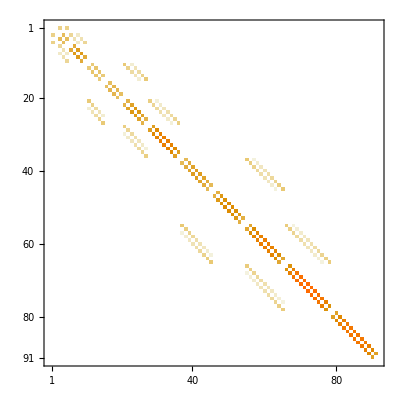

-Graphics-

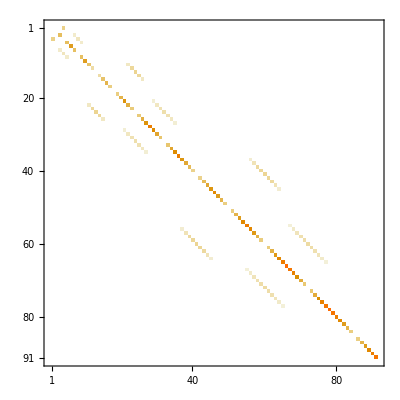

```mathematica
numE=2;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->2}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
MatrixPlot[Abs[magx]]
MatrixPlot[Abs[magy]]
MatrixPlot[Abs[magz]]
```

Here we calculate the line strength operator, from which we may compute the line strengths and spontaneous decay rates between all possible pairs of states.

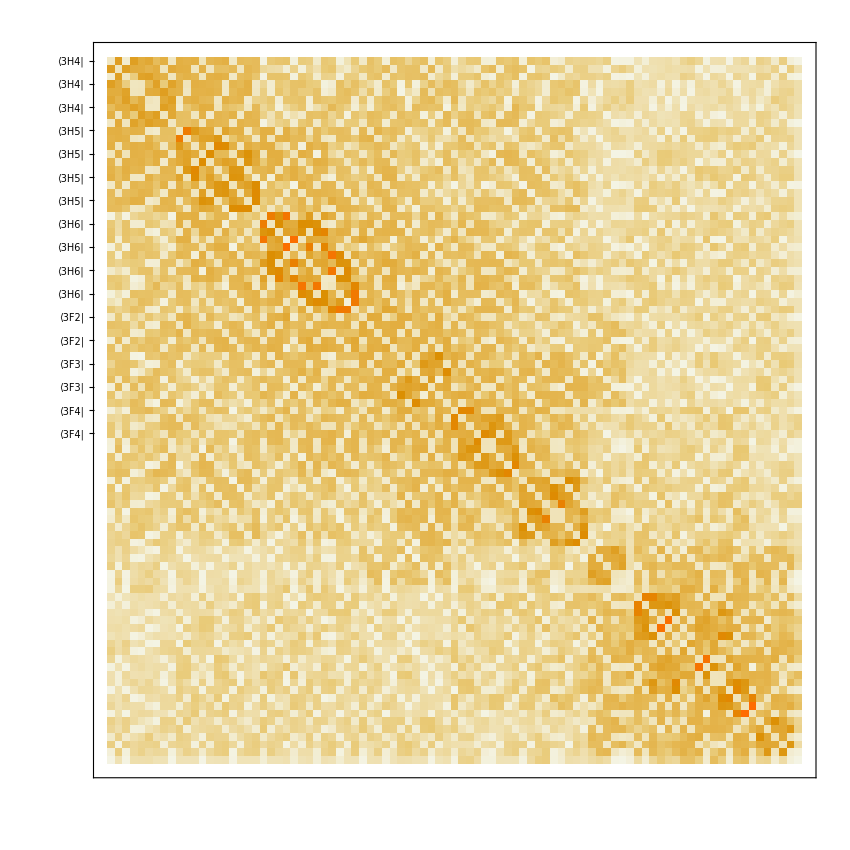

```mathematica
mag=MagDipLineStrength[eigensys,numE,"Reload MagOp"->False,"Units"->"SI"];
HamiltonianMatrixPlot[mag,simplerStateLabels,"Hover"->True,"Overlay Values"->False,ImageSize->850]
```

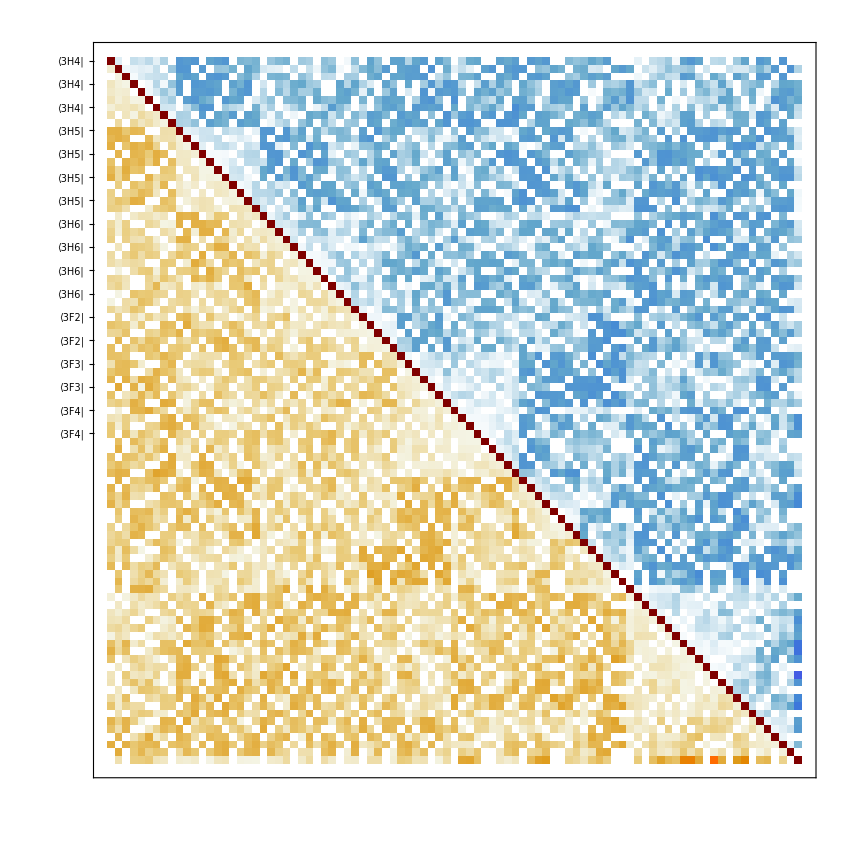

```mathematica
AMD=MagDipoleRates[eigensys,numE,"Units"->"SI","Lifetime"->False];
HamiltonianMatrixPlot[AMD,simplerStateLabels,"Hover"->True,"Overlay Values"->False,ImageSize->850]
```

```mathematica
GroundStateOscillatorStrength[eigensys,numE,"Units"->"SI"]
```

{Indeterminate,1.29684×10^-8,9.19719×10^-39,2.4383×10^-8,7.30793×10^-9,1.74557×10^-8,2.27762×10^-10,8.34608×10^-9,6.93424×10^-37,3.87554×10^-8,2.04866×10^-8,4.18463×10^-8,9.65129×10^-35,6.65117×10^-9,1.68933×10^-8,3.6989×10^-8,1.40044×10^-36,1.74372×10^-9,1.37507×10^-9,1.88143×10^-9,7.7114×10^-40,2.1953×10^-10,4.48275×10^-10,6.56952×10^-10,1.4401×10^-38,1.49198×10^-10,1.02514×10^-10,1.2212×10^-36,2.74292×10^-10,1.489×10^-10,2.62752×10^-38,4.264×10^-14,2.29527×10^-10,2.48776×10^-36,1.22402×10^-9,1.89967×10^-10,1.06234×10^-37,1.45296×10^-9,9.5269×10^-10,2.92972×10^-11,6.04375×10^-10,2.39702×10^-9,9.15134×10^-38,7.66174×10^-10,1.60468×10^-10,9.2513×10^-38,2.04312×10^-11,3.6931×10^-10,4.49393×10^-10,1.23399×10^-37,7.10733×10^-38,7.89438×10^-10,3.75288×10^-10,1.26926×10^-9,1.72723×10^-37,1.16646×10^-9,4.55664×10^-10,1.43339×10^-9,2.82101×10^-37,1.30278×10^-36,8.0138×10^-11,4.34892×10^-11,5.89616×10^-11,9.04478×10^-11,4.34379×10^-11,2.63503×10^-10,9.95528×10^-39,2.45301×10^-38,2.67022×10^-38,5.39724×10^-14,3.94346×10^-37,1.16573×10^-12,2.04726×10^-12,6.59743×10^-12,1.23931×10^-15,9.19628×10^-11,3.66212×10^-10,6.86197×10^-11,3.60383×10^-38,1.6353×10^-12,2.12716×10^-12,3.011×10^-39,6.23806×10^-12,6.04773×10^-11,2.9626×10^-38,2.37695×10^-10,7.56016×10^-11,7.25185×10^-36,4.20826×10^-10,2.96641×10^-37,7.31113×10^-39}

```mathematica
MagDipLineStrength[eigensys,numE,"Units"->"Atomic","States"->1]
```

```mathematica
(*Here we turn from atomic units to SI*)
μ0=4π×10^-7;
hPlanck=6.626*10^-34;
μB=9.274×10^-24;
me=9.109×10^-31;
cLight=2.998*10^8;
eCharge=1.602*10^-19;

{minλ,maxλ}={300,10000};
minfMD=0.015;
maxLen=20;

{Sx,Sy,Sz}=ConjugateTranspose[allEigen].#.allEigen&/@{magx,magy,magz};
(*The factor of 4 is need to account for the change of units from atomic to SI.*)
SMDALL=4*μB^2*(Abs[Sx]^2+Abs[Sy]^2+Abs[Sz]^2);
SMDGS=SMDALL[[;;,1]];
(*calculate transition wavelengths from excited to ground states*)
energyDifferences=Outer[Subtract,eigenEnergies,eigenEnergies];
(*since we are using the psedo-energy unit of cm^-1 the wavelength (in cm) is simply the reciprocal of the energy difference*)
transitionWaveLengthsInMeters=0.01/energyDifferences;
transitionWaveLengthsInNanoMeters=10^9*transitionWaveLengthsInMeters;
(*Here we only calculate the line strengths between the ground state and the excited states*)
groundStateEnergyDifferences=energyDifferences[[;;,1]];
groundStateTransitionWavelenghtsInMeters=transitionWaveLengthsInMeters[[;;,1]];
groundStateTransitionWavelenghtsInNanometers=transitionWaveLengthsInNanoMeters[[;;,1]];
(*under our SLJM description all degeneracy has been lifted, except in the case of odd number of electrons in which case Kramer's geneneracy remains in place*)
gKramers=If[OddQ[numE],2,1];
(*The units of the line strength are (J/T)^2*)
fMDGS=(8 π^2 me)/(3 h e^2 c)1/gKramers(1/groundStateTransitionWavelenghtsInMeters)*SMDGS ;
(*For completeness we may also compute the line strengths between all pairs of states*)
fMDALL=(8 π^2 me)/(3 h e^2 c)1/gKramers(1/transitionWaveLengthsInMeters)*SMDALL;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Let us also calculate what would be the spontaneous transition rates .

```mathematica
AMD=16 π^3 μ0/(3 hPlanck)*1/gKramers(1/transitionWaveLengthsInMeters^3)*SMDALL;
naturalLifetimes=1/AMD;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
lowToHigh=Reverse[Ordering[fMD]];
tabular=Transpose[{Last/@truncatedStates,
Round[#,1]&/@groundStateTransitionWavelenghtsInNanometers,
Round[#,1]&/@eigenEnergies,
ScientificForm[#,2]&/@(fMD*10^8)}];
tabular=tabular[[lowToHigh]];
tabular=Select[tabular,And[minλ<=#[[2]]<=maxλ,ToExpression[ToString[#[[-2]]]]>=minfMD]&];
tabular=tabular[[;;Min[Length[tabular],maxLen]]];
Grid[Prepend[tabular,{"ψ2","λ/nm","ΔE/cm^-1","fMD X 10^8"}],Frame->All]
```

Ordering::normal: Nonatomic expression expected at position 1 in Ordering[fMD].

Transpose::nmtx: The first two levels of «1» cannot be transposed.

Part::pkspec1: The expression Ordering[fMD] cannot be used as a part specification.

Part::partw: Part 2 of Transpose[{{0.14 RowBox+0.31 RowBox+0.88 RowBox+0.31 RowBox,0.11 RowBox+0.34 RowBox-0.61 RowBox+0.61 RowBox-0.34 RowBox,0.09 RowBox+0.41 RowBox+0.52 RowBox-0.32 RowBox+0.52 RowBox+0.41 RowBox,«6»,-0.25 RowBox-0.89 RowBox+0.2 RowBox-0.25 RowBox,«81»},{«15»,«10»},«1»,100000000 fMD}] does not exist.

Part::partw: Part -2 of Transpose[{{0.14 RowBox+0.31 RowBox+0.88 RowBox+0.31 RowBox,0.11 RowBox+0.34 RowBox-0.61 RowBox+0.61 RowBox-0.34 RowBox,0.09 RowBox+0.41 RowBox+0.52 RowBox-0.32 RowBox+0.52 RowBox+0.41 RowBox,«6»,-0.25 RowBox-0.89 RowBox+0.2 RowBox-0.25 RowBox,«81»},{«15»,«10»},«1»,100000000 fMD}] does not exist.

Transpose::nmtx: The first two levels of {{0.14 RowBox+0.31 RowBox+0.88 RowBox+0.31 RowBox,«9»,«81»},{ComplexInfinity,139857,105337,72569,54791,45267,30002,22521,21612,4703,«81»},{0,72,95,138,183,221,333,444,463,2126,«81»},100000000 fMD} cannot be transposed.

Part::partw: Part -2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Ordering::normal: Nonatomic expression expected at position 1 in Ordering[fMD].

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Grid[{ψ2,λ/nm,ΔE/cm^-1,fMD X 10^8},Frame→All]

The resulting data we save to a list that has elements of the form 
{i, f, label_i, label_f, E_i, E_f, λ_if, AMD_if, τ_if }
Where 
i is the index of the initial eigenvector,
f the index of the final eigenvector, 
label_i the coarse label for state i, 
label_j the coarse label for state j,
E_i the energy of state i (in cm^-1, rounded to a precision of 1 cm^-1),
E_f the energy of state j (in cm^-1, rounded to a precision of 1 cm^-1),
λ_ij the vacuum wavelength (in nm) of the transition between the two states,
 τ_if the vacuum natural radiative lifetime of the transition in units of s,
 and AMD the spontaneous transition rate in vacuum units of 1/s.

```mathematica
(*Options[RoundValueWithUncertainty]={"SetPrecision"->False};
RoundValueWithUncertainty::usage="RoundValueWithUncertainty[x,dx] given a number x together with an uncertainty dx this function rounds x to the first significant figure of dx and also rounds dx to have a single significant figure. 
The returned value is a list with the form {roundedX, roundedDx}.
The option \"SetPrecision\" can be used to control whether the Mathematica precision of x and dx is also set accordingly to these rules, otherwise the rounded numbers still have the original precision of the input values. 
If the position of the first significant figure of x is after the position of the first significant figure of dx, the function returns {0,dx} with dx rounded to one significant figure.";
RoundValueWithUncertainty[x_,dx_,OptionsPattern[]]:=Module[
{xExpo,dxExpo,sigFigs,roundedX,roundedDx,returning},
(
xExpo=RealDigits[x][[2]];
dxExpo=RealDigits[dx][[2]];
sigFigs=xExpo-dxExpo+1;
{roundedX,roundedDx}=If[sigFigs<=0,
{0.,N@RoundToSignificantFigures[dx,1]},
N[
{
RoundToSignificantFigures[x,xExpo-dxExpo+1],
RoundToSignificantFigures[dx,1]}
]
];
returning=If[
OptionValue["SetPrecision"],
{SetPrecision[roundedX,Max[1,sigFigs]],
SetPrecision[roundedDx,1]},
{roundedX,roundedDx}
];
Return[returning]
)
];

RoundToSignificantFigures::usage="RoundToSignificantFigures[x, sigFigs] rounds x so that it only has sigFigs significant figures.";
RoundToSignificantFigures[x_,sigFigs_]:=Sign[x]*N[FromDigits[RealDigits[x,10,sigFigs]]];*)

(*Options[FormatTable]={"Header"->""};
FormatTable::usage="FormatTable[aList] takes aList with lists as elements and formats it to create a succint textual representation of the numbers it contains. This is useful for removing padding zeroes that may be present when exporting data including numbers.
The option \"Header\" can be given to override the header that the resulting string has.";
FormatTable[aTable_List,OptionsPattern[]]:=Module[{formatted,riffled,idx},(
formatted=
Table[
(
riffled=Riffle[ToString[#,CForm]&/@aTable[[idx]],","];
StringJoin[riffled]
),
{idx,1,Length[aTable]}
];
formatted=StringJoin[Riffle[formatted,"\n"]];
If[Not[OptionValue["Header"]===""],
formatted=StringJoin[StringRiffle[ToString[#,CForm]&/@header,","]]<>"\n"<>formatted;
];
Return[formatted]
)
];*)
```

```mathematica
(*Assuming an uncertianto of 1 K in both energies used to calculate the wavelength*)
λuncertainty=√2*transitionWaveLengthsInNanoMeters^2*10^-7;

header={"ψi:simple","ψf:simple","ψi:idx","ψf:idx","Ei/K","Ef/K","λ/nm","Δλ/nm","τ/s","AMD/s^-1"};
numEigenvecs=Length[eigensys];
roundedEnergies=Round[eigenEnergies];
simpleFromTo=Outer[{#1,#2}&,simplerStateLabels,simplerStateLabels];
fromTo=Outer[{#1,#2}&,Range[numEigenvecs],Range[numEigenvecs]];
energyPairs=Outer[{#1,#2}&,roundedEnergies,roundedEnergies];
allTransitions={simpleFromTo,
fromTo,
energyPairs,
transitionWaveLengthsInNanoMeters,
λuncertainty,
AMD,
lifetimes
};
allTransitions=(Flatten/@Transpose[Flatten[#,1]&/@allTransitions]);
allTransitions=Select[allTransitions,#[[3]]!=#[[4]]&];
allTransitions=Select[allTransitions,#[[10]]>0&];
allTransitions=Transpose[allTransitions];
(*round things up*)
{roundedWaves,roundedDeltas}=Transpose[MapThread[RoundValueWithUncertainty,{allTransitions[[7]],allTransitions[[8]]}]];
allTransitions[[7]]=roundedWaves;
allTransitions[[8]]=roundedDeltas;
allTransitions[[9]]=RoundToSignificantFigures[#,3]&/@(allTransitions[[9]]);
allTransitions[[10]]=RoundToSignificantFigures[#,3]&/@(allTransitions[[10]]);
finalTable=Transpose[allTransitions];
finalTable=Prepend[finalTable,header];
(*finalTableString=FormatTable[finalTable,"Header"->header];*)
fname="Pr in LaF3 - M1.zip";
key=StringReplace[fname,".zip"->".m"];
Export[fname,<|key->finalTable|>];
```

```mathematica
RoundToSignificantFigures[12312,12]
```

12312

```mathematica
Length[finalTable]
```

4096

```mathematica
Export["final.xls",finalTable]
```

final.xls

```mathematica
Max[Last/@Import[fname,"Pr in LaF3 - M1.m"][[2;;]]]
```

4.×10^37

```mathematica
finalStrings=
Table[
StringJoin[Riffle[ToString[#,CForm]&/@finalTable[[i]],","]]
,{i,1,Length[finalTable]}];
finalStrings=StringJoin[Riffle[finalStrings,"\n"]];
(*finalStrings="{"<>finalStrings<>"}";*)
Export["stringss.m",finalStrings,"Text"];
```

```mathematica
data=Import["Pr in LaF3 - M1 transitions.m","CSV"][[2;;]];
```

```mathematica
Dataset[data]
```

Dataset[<>]

```mathematica
strings[[1]]
```

"3H4","3H4",2,1,72,0,1.4e5,3.e3,0.0000442,2.26e4

```mathematica
ExportMZip["Pr in LaF3 - M1 transitions.m",finalTable]
```

Pr in LaF3 - M1 transitions.zip

{"3H4","3H4",2,1,72,0,140000.,3000.,0.0000442,22600.,"3H4","3H4",3,1,95,0,105000.,2000.,5.03e-35,1.9900000000000002e34,"3H4","3H4",3,2,95,72,430000.,30000.,1.44e-6,696000.,"3H4","3H4",4,1,138,0,72600.,700.,0.000309,3240.,"3H4","3H4",4,2,138,72,151000.,3000.,7.860000000000001e-6,127000.,"3H4","3H4",4,3,138,95,233000.,8000.,1.22e-9,8.17e8,"3H4","3H4",5,1,183,0,54800.,400.,0.00016199999999999998,6160.,"3H4","3H4",5,2,183,72,90000.,1000.,0.0000313,32000.,"3H4","3H4",5,3,183,95,114000.,2000.,0.0000604,16600.,"3H4","3H4",5,4,183,138,224000.,7000.,1.51e-33,6.64e32}

```mathematica
SetPrecision[100000.123123,2]
```

100000.

```mathematica
formattedNumber=ExportString[{anum},"CSV","FieldSeparators"->"","NumberFormat"->(StringJoin[{"%.",ToString[Precision[anum]],"g"}]&)]
```

1.9900000000000002e34

```mathematica
anum=finalTable[[3]][[-1]];
aroundnum=NumberForm[anum,{Infinity,1}]
```

2.0×10^34

```mathematica
ToString[SetPrecision[finalTable[[3]][[-1]],5],CForm]
```

1.99e34

```mathematica
Export["anum.m",CForm[finalTable[[3]][[-1]]]]
```

anum.m

```mathematica
Prepend[Transpose[allTransitions][[;;10]],header]//TableForm
```

ψ_i | ψ_f | initial_state_idx | final_state_idx | Ei/cm^-1 | Ef/cm^-1 | λ/nm | Δλ/nm | τ/s | A_MD/s^-1
3H4 | 3H4 | 2 | 1 | 72 | 0 | 140000. | 3000. | 0.0000442 | 22600.
3H4 | 3H4 | 3 | 1 | 95 | 0 | 105000. | 2000. | 5.03×10^-35 | 1.99×10^34
3H4 | 3H4 | 3 | 2 | 95 | 72 | 430000. | 30000. | 1.44×10^-6 | 696000.
3H4 | 3H4 | 4 | 1 | 138 | 0 | 72600. | 700. | 0.000309 | 3240.
3H4 | 3H4 | 4 | 2 | 138 | 72 | 151000. | 3000. | 7.86×10^-6 | 127000.
3H4 | 3H4 | 4 | 3 | 138 | 95 | 233000. | 8000. | 1.22×10^-9 | 8.17×10^8
3H4 | 3H4 | 5 | 1 | 183 | 0 | 54800. | 400. | 0.000162 | 6160.
3H4 | 3H4 | 5 | 2 | 183 | 72 | 90000. | 1000. | 0.0000313 | 32000.
3H4 | 3H4 | 5 | 3 | 183 | 95 | 114000. | 2000. | 0.0000604 | 16600.
3H4 | 3H4 | 5 | 4 | 183 | 138 | 224000. | 7000. | 1.51×10^-33 | 6.64×10^32

```mathematica
RoundValueWithUncertaintyAndSetPrecision[1123.23123,3.1]
```

{1100.,3.}

```mathematica
Export["testing.m",RoundValueWithUncertaintyAndSetPrecision[1123.23123,23.1]]
```

testing.m

```mathematica
Select[allTransitions,#[[-1]]<0&][[-1]]
```

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{3P2,1S0,90,91,22818.3,46964.5,-414.143,-9.89837×10^-29,-1.01027×10^28}

```mathematica
{minλ,maxλ}={300,1700};
takeOnly=20;

(*allTransitions=Select[allTransitions,And[#[[4]]>0,minλ<=#[[6]]<=maxλ]&];
allTransitions=SortBy[allTransitions,#[[5]]&];
Grid[Prepend[allTransitions[[;;takeOnly]],header],Frame->All]*)
```

ψ_i->ψ_f | ψ_i | ψ_f | A_MD/s^-1 | τ/s | λ/nm | i | j | Ei/cm^-1 | Ef/cm^-1
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 9.9 % 1I{6,-1}+9.9 % 1I{6,1}+36.9 % 3P{1,-1}+36.9 % 3P{1,1} | 5.53886 | 0.180543 | 394.095 | 91 | 80 | 46964.7 | 21590.2
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.2 % 1I{6,-3}+0.2 % 1I{6,3}+49.4 % 3P{1,-1}+49.4 % 3P{1,1} | 3.32608 | 0.300654 | 392.969 | 91 | 77 | 46964.7 | 21517.4
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.3 % 1I{6,-2}+0.3 % 1I{6,2}+0.1 % 1I{6,4}+99. % 3P{1,0} | 3.13244 | 0.31924 | 392.474 | 91 | 76 | 46964.7 | 21485.3
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 2.65496 | 0.376654 | 398.789 | 91 | 84 | 46964.7 | 21888.8
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 1.15869 | 0.863044 | 397.442 | 91 | 83 | 46964.7 | 21803.9
1D2→3F2 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 46.5 % 3F{2,-2}+46.5 % 3F{2,2}+1.5 % 3H{6,-2}+1.5 % 3H{6,2} | 0.741892 | 1.34791 | 837.912 | 67 | 35 | 17116.9 | 5182.5
1I6→1G4 | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 16.5 % 1G{4,-4}+21.4 % 1G{4,0}+16.5 % 1G{4,4}+12.4 % 3F{4,0} | 0.526187 | 1.90046 | 844.101 | 83 | 59 | 21803.9 | 9956.93
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 37.9 % 1I{6,-3}+10.6 % 1I{6,-1}+10.6 % 1I{6,1}+37.9 % 1I{6,3} | 0.517487 | 1.93242 | 391.014 | 91 | 73 | 46964.7 | 21390.2
1I6→1G4 | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 6.6 % 1G{4,-4}+41.4 % 1G{4,0}+6.6 % 1G{4,4}+21.7 % 3F{4,0} | 0.515803 | 1.93873 | 840.823 | 84 | 60 | 21888.8 | 9995.72
3F4→3H4 | 24.4 % 3F{4,-3}+11.8 % 3F{4,-1}+11.8 % 3F{4,1}+24.4 % 3F{4,3} | 1.3 % 1G{4,-2}+1.3 % 1G{4,2}+46.2 % 3H{4,-2}+46.2 % 3H{4,2} | 0.509121 | 1.96417 | 1466.6 | 54 | 7 | 7152.02 | 333.517
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 1.2 % 1D{2,-1}+1.2 % 1D{2,1}+47.8 % 3F{2,-1}+47.8 % 3F{2,1} | 0.492871 | 2.02893 | 834.384 | 68 | 36 | 17169.7 | 5184.8
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 42.3 % 3F{2,-1}+42.3 % 3F{2,1}+3.1 % 3H{6,-3}+3.1 % 3H{6,3} | 0.425296 | 2.3513 | 840.743 | 68 | 38 | 17169.7 | 5275.44
1D2→3F2 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 9.1 % 3F{2,-2}+66.5 % 3F{2,0}+9.1 % 3F{2,2}+3.3 % 3H{6,6} | 0.395407 | 2.52904 | 846.533 | 66 | 37 | 17082.4 | 5269.51
1D2→3F3 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 44.1 % 3F{3,-3}+4.7 % 3F{3,-1}+4.7 % 3F{3,1}+44.1 % 3F{3,3} | 0.383216 | 2.6095 | 953.405 | 67 | 44 | 17116.9 | 6628.2
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 1.1 % 3F{3,-3}+47. % 3F{3,-1}+47. % 3F{3,1}+1.1 % 3F{3,3} | 0.371738 | 2.69007 | 945.624 | 66 | 41 | 17082.4 | 6507.37
1D2→3F3 | 44.6 % 1D{2,-1}+44.6 % 1D{2,1}+4. % 3P{2,-1}+4. % 3P{2,1} | 31.6 % 3F{3,-2}+31.5 % 3F{3,0}+31.6 % 3F{3,2}+1.3 % 3F{4,4} | 0.369631 | 2.7054 | 961.093 | 65 | 40 | 16894.8 | 6489.97
1I6→1G4 | 13.7 % 1I{6,-6}+56.6 % 1I{6,0}+4. % 1I{6,2}+13.7 % 1I{6,6} | 24.6 % 1G{4,-3}+11.4 % 1G{4,-1}+11.4 % 1G{4,1}+24.6 % 1G{4,3} | 0.367658 | 2.71992 | 896.828 | 82 | 63 | 21666.3 | 10515.9
1I6→3H6 | 41. % 1I{6,-2}+14.5 % 1I{6,0}+41. % 1I{6,2}+0.8 % 3P{2,0} | 6.3 % 3H{6,-3}+42.7 % 3H{6,-1}+42.7 % 3H{6,1}+6.3 % 3H{6,3} | 0.366748 | 2.72667 | 579.119 | 79 | 24 | 21588.2 | 4320.64
1D2→3F3 | 44.5 % 1D{2,-2}+44.5 % 1D{2,2}+4.1 % 3P{2,-2}+4.1 % 3P{2,2} | 46.3 % 3F{3,-3}+1.1 % 3F{3,-1}+1.1 % 3F{3,1}+46.3 % 3F{3,3} | 0.366241 | 2.73044 | 958.706 | 64 | 39 | 16887.1 | 6456.39
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 15. % 3F{3,-2}+64.3 % 3F{3,0}+15. % 3F{3,2}+1. % 3H{6,4} | 0.358472 | 2.78962 | 966.918 | 66 | 45 | 17082.4 | 6740.26

```mathematica
truncatedStates=ParseStatesByNumBasisVecs[eigensys,basis,4,0.001,"Coefficients"->"Probabilities"];
```

```mathematica
{123,123,123,123}*100"%"
```

{12300 %,12300 %,12300 %,12300 %}

## Eu in LaF3

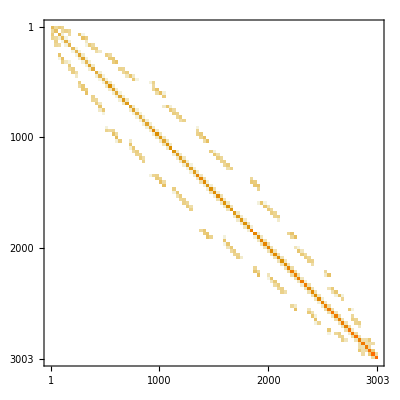

-Graphics-

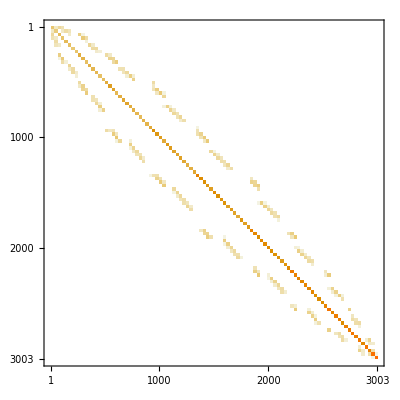

```mathematica
numE=6;
basis=BasisLSJMJ[numE];
prettybasis=PrettySaundersSLJmJ/@basis;
magOp=ReplaceInSparseArray[#,{gs->2}]&/@MagDipoleMatrixAssembly[numE];
{magx,magy,magz}=magOp;
MatrixPlot[Abs[magx]]
MatrixPlot[Abs[magy]]
MatrixPlot[Abs[magz]]
```

```mathematica
{rmsDifference,carnallEnergies,eigenEnergies,ln,
carnallAssignments,simplerStateLabels,eigensys,basis,truncatedStates}=Import["./examples/Eu in LaF3 - example.m"];
```

```mathematica
(*the eigenvectors as columns*)
allEigen=Transpose[Last/@eigensys];
```

```mathematica
Sx=ConjugateTranspose[allEigen].magx.allEigen;
Sy=ConjugateTranspose[allEigen].magy.allEigen;
Sz=ConjugateTranspose[allEigen].magz.allEigen;
(* line strent*)
lineStrength=Abs[Sx]^2+Abs[Sy]^2+Abs[Sz]^2;
```

```mathematica
MatrixPlot[lineStrength]
```

-Graphics-

```mathematica
μ0=4π×10^-7;
h=6.626*10^-34;
μB=9.274×10^-24;
me=9.109×10^-31;
c=2.998*10^8;
e=1.602*10^-19;

{minλ,maxλ}={300,10000};
minfMD=0.015;
maxLen=20;

{Sx,Sy,Sz}=ConjugateTranspose[allEigen].#.allEigen&/@{magx,magy,magz};
SMDALL=μB^2*(Abs[Sx]^2+Abs[Sy]^2+Abs[Sz]^2);
SMDGS=SMDALL[[;;,1]];
(*calculate transition wavelenghts from excited to ground states*)
energyDifferences=Outer[Subtract,eigenEnergies,eigenEnergies];
transitionWaveLengthsInMeters=1/energyDifferences/100;
transitionWaveLengthsInNanoMeters=10^9*transitionWaveLengthsInMeters;
groundStateEnergyDifferences=energyDifferences[[;;,1]];
groundStateTransitionWavelenghtsInMeters=transitionWaveLengthsInMeters[[;;,1]];
groundStateTransitionWavelenghtsInNanometers=groundStateTransitionWavelenghtsInMeters*10^9;
fMD=(8 π^2 me)/(3 h e^2 c)(1/groundStateTransitionWavelenghtsInMeters) ;
fMD=fMD*SMDGS;
AMD=16 π^3 μ0/(3 h)*(1/transitionWaveLengthsInMeters^3)*SMDALL;
lifetimes=1/AMD;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
lowToHigh=Reverse[Ordering[fMD]];
tabular=Transpose[{Last/@truncatedStates,
Round[#,1]&/@groundStateTransitionWavelenghtsInNanometers,
Round[#,1]&/@eigenEnergies,
ScientificForm[#,2]&/@(fMD*10^8)}];
tabular=tabular[[lowToHigh]];
tabular=Select[tabular,And[minλ<=#[[2]]<=maxλ,ToExpression[ToString[#[[-2]]]]>=minfMD]&];
tabular=tabular[[;;Min[Length[tabular],maxLen]]];
Grid[Prepend[tabular,{"ψ2","λ/nm","ΔE/cm^-1","fMD X 10^8"}],Frame->All]
```

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

ψ2 | λ/nm | ΔE/cm^-1 | fMD X 10^8
-0.42 3H{5,-5}-0.53 3H{5,-1}-0.53 3H{5,1}-0.19 3H{5,3}-0.42 3H{5,5} | 4566 | 2190 | 4.2
-0.25 3H{5,-4}-0.89 3H{5,0}+0.2 3H{5,2}-0.25 3H{5,4} | 4703 | 2126 | 3.9
-0.62 3H{5,-5}-0.19 3H{5,-3}-0.27 3H{5,-1}+0.27 3H{5,1}+0.19 3H{5,3}+0.62 3H{5,5} | 4315 | 2317 | 3.7
0.31 3H{5,-3}-0.61 3H{5,-1}+0.61 3H{5,1}-0.31 3H{5,3}-0.17 3H{5,5} | 4635 | 2158 | 2.
0.29 3H{5,-4}+0.63 3H{5,-2}+0.12 3H{5,0}+0.63 3H{5,2}+0.29 3H{5,4} | 4358 | 2295 | 1.7
-0.24 3H{5,-5}-0.53 3H{5,-3}+0.39 3H{5,-1}+0.39 3H{5,1}-0.53 3H{5,3}-0.24 3H{5,5} | 4368 | 2289 | 6.7×10^-1
-0.21 3F{3,-3}+0.66 3F{3,-1}+0.66 3F{3,1}-0.21 3F{3,3} | 1520 | 6579 | 2.4×10^-1
-0.29 3H{5,-5}+0.6 3H{5,-3}+0.23 3H{5,-1}-0.23 3H{5,1}-0.6 3H{5,3}+0.29 3H{5,5} | 3938 | 2540 | 1.9×10^-1
-0.08 3F{2,1}+0.5 3H{5,-5}-0.41 3H{5,-3}-0.25 3H{5,-1}-0.25 3H{5,1}-0.41 3H{5,3}+0.5 3H{5,5} | 4146 | 2412 | 1.7×10^-1
0.65 3F{2,-1}-0.65 3F{2,1}+0.14 3H{6,-5}+0.17 3H{6,-3}-0.17 3H{6,3}-0.14 3H{6,5} | 1896 | 5275 | 1.5×10^-1
0.32 1G{4,-3}+0.46 1G{4,-1}+0.46 1G{4,1}+0.32 1G{4,3}+0.24 3F{4,-3}+0.35 3F{4,-1}+0.35 3F{4,1}+0.24 3F{4,3} | 1007 | 9927 | 1.4×10^-1
0.59 3H{5,-4}-0.22 3H{5,-2}-0.42 3H{5,0}-0.22 3H{5,2}+0.59 3H{5,4} | 4103 | 2437 | 1.4×10^-1
-0.29 1G{4,-3}+0.21 1G{4,-1}+0.21 1G{4,1}-0.29 1G{4,3}+0.49 3F{4,-3}-0.34 3F{4,-1}-0.34 3F{4,1}+0.49 3F{4,3} | 1398 | 7152 | 1.3×10^-1
-0.68 3F{2,-2}+0.68 3F{2,2}+0.12 3H{6,2} | 1930 | 5182 | 1.2×10^-1
-0.52 1G{4,-1}+0.52 1G{4,1}+0.12 1G{4,3}-0.44 3F{4,-1}+0.44 3F{4,1} | 1024 | 9762 | 1.2×10^-1
0.68 3F{3,-3}-0.68 3F{3,3}+0.08 3F{4,3} | 1549 | 6456 | 9.5×10^-2
0.41 1G{4,-3}-0.41 1G{4,3}-0.57 3F{4,-3}+0.57 3F{4,3}+0.09 3H{4,3} | 1422 | 7034 | 7.9×10^-2
-0.66 3F{3,-3}-0.22 3F{3,-1}-0.22 3F{3,1}-0.66 3F{3,3} | 1509 | 6628 | 7.7×10^-2
0.25 3H{6,-3}-0.65 3H{6,-1}+0.65 3H{6,1}-0.25 3H{6,3} | 2315 | 4321 | 6.6×10^-2
-0.69 3F{3,-1}+0.69 3F{3,1}+0.1 3H{6,5} | 1537 | 6507 | 6.×10^-2

-Graphics-

```mathematica
truncatedStates=ParseStatesByNumBasisVecs[eigensys,basis,4,0.001,"Coefficients"->"Amplitudes"];
simpleFromTo=Outer[#1->#2&,simplerStateLabels,simplerStateLabels];
fromTo=Outer[{#1,#2}&,Last/@truncatedStates,Last/@truncatedStates];
indexPairs=Outer[{#1,#2}&,Range[Length[eigensys]],Range[Length[eigensys]]];
energyPairs=Outer[{#1,#2}&,eigenEnergies,eigenEnergies];
```

```mathematica
eigenVec=eigensys[[50,2]];
mags=Abs[eigenVec];
picker=#>=0.15&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
```

-0.174002 3P1{0,0}+0.22185 3P3{0,0}+0.251049 3P6{0,0}-0.543762 5D1{0,0}-0.18059 5D2{0,0}+0.676211 5D3{0,0}-0.243443 7F{0,0}

```mathematica
eigenVec=eigensys[[2,2]];
mags=Abs[eigenVec];
picker=#>=0.1&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
eigenVec=eigensys[[3,2]];
mags=Abs[eigenVec];
picker=#>=0.1&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
eigenVec=eigensys[[4,2]];
mags=Abs[eigenVec];
picker=#>=0.1&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
```

0.169189 5D1{1,0}-0.147174 5D3{1,0}-0.966431 7F{1,0}

-0.119731 5D1{1,-1}+0.119731 5D1{1,1}+0.104271 5D3{1,-1}-0.104271 5D3{1,1}+0.6833 7F{1,-1}-0.6833 7F{1,1}

-0.120282 5D1{1,-1}-0.120282 5D1{1,1}+0.104829 5D3{1,-1}+0.104829 5D3{1,1}+0.686002 7F{1,-1}+0.686002 7F{1,1}

```mathematica
eigenVec=eigensys[[2,2]];
mags=Abs[eigenVec];
picker=#>=0.1&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
eigenVec=eigensys[[50,2]];
mags=Abs[eigenVec];
picker=#>=0.1&/@mags;
Pick[eigenVec,picker].Pick[prettybasis,picker]
```

0.169189 5D1{1,0}-0.147174 5D3{1,0}-0.966431 7F{1,0}

-0.174002 3P1{0,0}+0.22185 3P3{0,0}+0.251049 3P6{0,0}-0.543762 5D1{0,0}-0.18059 5D2{0,0}+0.676211 5D3{0,0}-0.243443 7F{0,0}

```mathematica
{energy1,eigenVec1}=eigensys[[2]];
{energy2,eigenVec2}=eigensys[[50]];
```

```mathematica
Dimensions[AMD]
```

{3003,3003}

```mathematica
wavelengthinm=1/(energy2-energy1)1/100;
```

```mathematica
16 π^3 μ0/(3 h)0.1159/wavelengthinm^3 μB^2
```

15.2837

```mathematica
AMD[[50,2;;4]]//Total
```

14.2415

```mathematica
(8 π^2 me)/(3 h e^2 c)(1/wavelengthinm)*SMDALL[[2;;5,50]]
```

{2.48513×10^-8,2.48333×10^-8,2.51015×10^-8,1.00438×10^-38}

```mathematica
header={"ψ_i->ψ_f","ψ_i","ψ_f",Tooltip["A_MD/s^-1","Spontaneous Decay Rate"],Tooltip["τ/s","Radiative Lifetime"],Tooltip["λ/nm","Emission Wavelength"],"i","j","Ei/cm^-1","Ef/cm^-1"};
{minλ,maxλ}={300,1700};
takeOnly=20;
allTransitions={simpleFromTo,
fromTo,
AMD,
lifetimes,
transitionWaveLengthsInNanoMeters,
indexPairs,
energyPairs};
allTransitions=(Flatten/@Transpose[Flatten[#,1]&/@allTransitions]);

allTransitions=Select[allTransitions,And[#[[4]]>0,minλ<=#[[6]]<=maxλ]&];
allTransitions=SortBy[allTransitions,#[[5]]&];
Grid[Prepend[allTransitions[[;;takeOnly]],header],Frame->All]
```

ψ_i->ψ_f | ψ_i | ψ_f | A_MD/s^-1 | τ/s | λ/nm | i | j | Ei/cm^-1 | Ef/cm^-1
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 9.9 % 1I{6,-1}+9.9 % 1I{6,1}+36.9 % 3P{1,-1}+36.9 % 3P{1,1} | 5.53886 | 0.180543 | 394.095 | 91 | 80 | 46964.7 | 21590.2
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.2 % 1I{6,-3}+0.2 % 1I{6,3}+49.4 % 3P{1,-1}+49.4 % 3P{1,1} | 3.32608 | 0.300654 | 392.969 | 91 | 77 | 46964.7 | 21517.4
1S0→3P1 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 0.3 % 1I{6,-2}+0.3 % 1I{6,2}+0.1 % 1I{6,4}+99. % 3P{1,0} | 3.13244 | 0.31924 | 392.474 | 91 | 76 | 46964.7 | 21485.3
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 2.65496 | 0.376654 | 398.789 | 91 | 84 | 46964.7 | 21888.8
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 1.15869 | 0.863044 | 397.442 | 91 | 83 | 46964.7 | 21803.9
1D2→3F2 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 46.5 % 3F{2,-2}+46.5 % 3F{2,2}+1.5 % 3H{6,-2}+1.5 % 3H{6,2} | 0.741892 | 1.34791 | 837.912 | 67 | 35 | 17116.9 | 5182.5
1I6→1G4 | 16.6 % 1I{6,-5}+22.7 % 1I{6,-1}+22.7 % 1I{6,1}+16.6 % 1I{6,5} | 16.5 % 1G{4,-4}+21.4 % 1G{4,0}+16.5 % 1G{4,4}+12.4 % 3F{4,0} | 0.526187 | 1.90046 | 844.101 | 83 | 59 | 21803.9 | 9956.93
1S0→1I6 | 98.9 % 1S{0,0}+1.1 % 3P{0,0} | 37.9 % 1I{6,-3}+10.6 % 1I{6,-1}+10.6 % 1I{6,1}+37.9 % 1I{6,3} | 0.517487 | 1.93242 | 391.014 | 91 | 73 | 46964.7 | 21390.2
1I6→1G4 | 43.2 % 1I{6,-6}+5.8 % 1I{6,-4}+5.8 % 1I{6,4}+43.2 % 1I{6,6} | 6.6 % 1G{4,-4}+41.4 % 1G{4,0}+6.6 % 1G{4,4}+21.7 % 3F{4,0} | 0.515803 | 1.93873 | 840.823 | 84 | 60 | 21888.8 | 9995.72
3F4→3H4 | 24.4 % 3F{4,-3}+11.8 % 3F{4,-1}+11.8 % 3F{4,1}+24.4 % 3F{4,3} | 1.3 % 1G{4,-2}+1.3 % 1G{4,2}+46.2 % 3H{4,-2}+46.2 % 3H{4,2} | 0.509121 | 1.96417 | 1466.6 | 54 | 7 | 7152.02 | 333.517
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 1.2 % 1D{2,-1}+1.2 % 1D{2,1}+47.8 % 3F{2,-1}+47.8 % 3F{2,1} | 0.492871 | 2.02893 | 834.384 | 68 | 36 | 17169.7 | 5184.8
1D2→3F2 | 86.5 % 1D{2,0}+0.6 % 1D{2,2}+2.1 % 3F{2,0}+8.9 % 3P{2,0} | 42.3 % 3F{2,-1}+42.3 % 3F{2,1}+3.1 % 3H{6,-3}+3.1 % 3H{6,3} | 0.425296 | 2.3513 | 840.743 | 68 | 38 | 17169.7 | 5275.44
1D2→3F2 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 9.1 % 3F{2,-2}+66.5 % 3F{2,0}+9.1 % 3F{2,2}+3.3 % 3H{6,6} | 0.395407 | 2.52904 | 846.533 | 66 | 37 | 17082.4 | 5269.51
1D2→3F3 | 43.1 % 1D{2,-2}+43.1 % 1D{2,2}+4.6 % 3P{2,-2}+4.6 % 3P{2,2} | 44.1 % 3F{3,-3}+4.7 % 3F{3,-1}+4.7 % 3F{3,1}+44.1 % 3F{3,3} | 0.383216 | 2.6095 | 953.405 | 67 | 44 | 17116.9 | 6628.2
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 1.1 % 3F{3,-3}+47. % 3F{3,-1}+47. % 3F{3,1}+1.1 % 3F{3,3} | 0.371738 | 2.69007 | 945.624 | 66 | 41 | 17082.4 | 6507.37
1D2→3F3 | 44.6 % 1D{2,-1}+44.6 % 1D{2,1}+4. % 3P{2,-1}+4. % 3P{2,1} | 31.6 % 3F{3,-2}+31.5 % 3F{3,0}+31.6 % 3F{3,2}+1.3 % 3F{4,4} | 0.369631 | 2.7054 | 961.093 | 65 | 40 | 16894.8 | 6489.97
1I6→1G4 | 13.7 % 1I{6,-6}+56.6 % 1I{6,0}+4. % 1I{6,2}+13.7 % 1I{6,6} | 24.6 % 1G{4,-3}+11.4 % 1G{4,-1}+11.4 % 1G{4,1}+24.6 % 1G{4,3} | 0.367658 | 2.71992 | 896.828 | 82 | 63 | 21666.3 | 10515.9
1I6→3H6 | 41. % 1I{6,-2}+14.5 % 1I{6,0}+41. % 1I{6,2}+0.8 % 3P{2,0} | 6.3 % 3H{6,-3}+42.7 % 3H{6,-1}+42.7 % 3H{6,1}+6.3 % 3H{6,3} | 0.366748 | 2.72667 | 579.119 | 79 | 24 | 21588.2 | 4320.64
1D2→3F3 | 44.5 % 1D{2,-2}+44.5 % 1D{2,2}+4.1 % 3P{2,-2}+4.1 % 3P{2,2} | 46.3 % 3F{3,-3}+1.1 % 3F{3,-1}+1.1 % 3F{3,1}+46.3 % 3F{3,3} | 0.366241 | 2.73044 | 958.706 | 64 | 39 | 16887.1 | 6456.39
1D2→3F3 | 44.2 % 1D{2,-1}+44.2 % 1D{2,1}+4.3 % 3P{2,-1}+4.3 % 3P{2,1} | 15. % 3F{3,-2}+64.3 % 3F{3,0}+15. % 3F{3,2}+1. % 3H{6,4} | 0.358472 | 2.78962 | 966.918 | 66 | 45 | 17082.4 | 6740.26

```mathematica
{123,123,123,123}*100"%"
```

{12300 %,12300 %,12300 %,12300 %}